```mathematica
RandomTable[n_] := Table[Random[],{i,1,n}]
```

```mathematica
RandomTable[10]
```

{0.951202,0.762691,0.174433,0.421746,0.105639,0.133954,0.159155,0.816702,0.313286,0.592355}

```mathematica
RandomTablePairs[A_,k_] := Table[{A[[i]],A[[i+k]]},{i,1,Length[A]-k}];
```

```mathematica
RandomTablePairs[RandomTable[1000],2]
```

{{0.984352,0.112635},{0.519986,0.264558},{0.112635,0.343184},{0.264558,0.00801056},{0.343184,0.0652964},{0.00801056,0.304329},{0.0652964,0.672186},{0.304329,0.220784},{0.672186,0.0359265},{0.220784,0.596036},{0.0359265,0.737691},{0.596036,0.109511},{0.737691,0.084724},{0.109511,0.833344},{0.084724,0.563258},{0.833344,0.687765},{0.563258,0.979085},{0.687765,0.69939},{0.979085,0.404103},{0.69939,0.871063},{0.404103,0.665799},{0.871063,0.107035},{0.665799,0.419751},{0.107035,0.351077},{0.419751,0.553164},{0.351077,0.842477},{0.553164,0.0765675},{0.842477,0.343067},{0.0765675,0.487867},{0.343067,0.538148},{0.487867,0.404381},{0.538148,0.122283},{0.404381,0.451941},{0.122283,0.942112},{0.451941,0.66669},{0.942112,0.0127714},{0.66669,0.367217},{0.0127714,0.108768},{0.367217,0.103432},{0.108768,0.325006},{0.103432,0.388132},{0.325006,0.409378},{0.388132,0.699329},{0.409378,0.453943},{0.699329,0.722333},{0.453943,0.302343},{0.722333,0.279578},{0.302343,0.102866},{0.279578,0.16917},{0.102866,0.459866},{0.16917,0.203011},{0.459866,0.7598},{0.203011,0.681302},{0.7598,0.921718},{0.681302,0.79863},{0.921718,0.637517},{0.79863,0.229361},{0.637517,0.979606},{0.229361,0.131939},{0.979606,0.624746},{0.131939,0.862144},{0.624746,0.870839},{0.862144,0.0285073},{0.870839,0.299739},{0.0285073,0.474012},{0.299739,0.461461},{0.474012,0.329178},{0.461461,0.845796},{0.329178,0.751678},{0.845796,0.159118},{0.751678,0.0495998},{0.159118,0.74293},{0.0495998,0.582509},{0.74293,0.699252},{0.582509,0.846589},{0.699252,0.98313},{0.846589,0.901207},{0.98313,0.777533},{0.901207,0.0479595},{0.777533,0.345613},{0.0479595,0.671846},{0.345613,0.797927},{0.671846,0.91602},{0.797927,0.720867},{0.91602,0.809702},{0.720867,0.927088},{0.809702,0.887513},{0.927088,0.421128},{0.887513,0.33569},{0.421128,0.465627},{0.33569,0.558335},{0.465627,0.575332},{0.558335,0.584012},{0.575332,0.306509},{0.584012,0.508735},{0.306509,0.832402},{0.508735,0.00150295},{0.832402,0.607257},{0.00150295,0.662146},{0.607257,0.849272},{0.662146,0.100296},{0.849272,0.829724},{0.100296,0.614186},{0.829724,0.503659},{0.614186,0.428451},{0.503659,0.0317969},{0.428451,0.698166},{0.0317969,0.782791},{0.698166,0.618749},{0.782791,0.104708},{0.618749,0.810653},{0.104708,0.361663},{0.810653,0.283059},{0.361663,0.639081},{0.283059,0.252319},{0.639081,0.786331},{0.252319,0.699048},{0.786331,0.332572},{0.699048,0.743584},{0.332572,0.953929},{0.743584,0.697545},{0.953929,0.725314},{0.697545,0.0814376},{0.725314,0.104657},{0.0814376,0.597249},{0.104657,0.89559},{0.597249,0.467251},{0.89559,0.600999},{0.467251,0.168798},{0.600999,0.863793},{0.168798,0.769085},{0.863793,0.818208},{0.769085,0.550048},{0.818208,0.759085},{0.550048,0.958431},{0.759085,0.456544},{0.958431,0.266989},{0.456544,0.120004},{0.266989,0.706113},{0.120004,0.670213},{0.706113,0.567941},{0.670213,0.787432},{0.567941,0.962529},{0.787432,0.716284},{0.962529,0.870396},{0.716284,0.0621178},{0.870396,0.881092},{0.0621178,0.611626},{0.881092,0.273148},{0.611626,0.166528},{0.273148,0.41384},{0.166528,0.0106276},{0.41384,0.10435},{0.0106276,0.302734},{0.10435,0.644756},{0.302734,0.19242},{0.644756,0.554302},{0.19242,0.543649},{0.554302,0.686324},{0.543649,0.735876},{0.686324,0.287313},{0.735876,0.423645},{0.287313,0.980211},{0.423645,0.0656626},{0.980211,0.719371},{0.0656626,0.636213},{0.719371,0.017682},{0.636213,0.349379},{0.017682,0.848975},{0.349379,0.574096},{0.848975,0.13659},{0.574096,0.737752},{0.13659,0.575827},{0.737752,0.407568},{0.575827,0.72275},{0.407568,0.727125},{0.72275,0.471477},{0.727125,0.104834},{0.471477,0.0779944},{0.104834,0.534705},{0.0779944,0.917176},{0.534705,0.561185},{0.917176,0.39167},{0.561185,0.798829},{0.39167,0.629863},{0.798829,0.137539},{0.629863,0.411459},{0.137539,0.733166},{0.411459,0.910491},{0.733166,0.501326},{0.910491,0.393777},{0.501326,0.383788},{0.393777,0.0615164},{0.383788,0.92723},{0.0615164,0.257187},{0.92723,0.646035},{0.257187,0.485689},{0.646035,0.519662},{0.485689,0.534437},{0.519662,0.91891},{0.534437,0.014212},{0.91891,0.414828},{0.014212,0.456442},{0.414828,0.384206},{0.456442,0.0970365},{0.384206,0.853643},{0.0970365,0.064772},{0.853643,0.585377},{0.064772,0.467174},{0.585377,0.716104},{0.467174,0.653313},{0.716104,0.85221},{0.653313,0.556682},{0.85221,0.214778},{0.556682,0.259536},{0.214778,0.468423},{0.259536,0.495166},{0.468423,0.287548},{0.495166,0.00234931},{0.287548,0.822387},{0.00234931,0.00947656},{0.822387,0.767886},{0.00947656,0.467913},{0.767886,0.903477},{0.467913,0.995265},{0.903477,0.353058},{0.995265,0.0114704},{0.353058,0.519272},{0.0114704,0.898228},{0.519272,0.499415},{0.898228,0.946698},{0.499415,0.933895},{0.946698,0.431054},{0.933895,0.783311},{0.431054,0.293385},{0.783311,0.0816849},{0.293385,0.874372},{0.0816849,0.568532},{0.874372,0.0338495},{0.568532,0.613262},{0.0338495,0.379206},{0.613262,0.280984},{0.379206,0.0315002},{0.280984,0.790875},{0.0315002,0.36973},{0.790875,0.513098},{0.36973,0.563588},{0.513098,0.887398},{0.563588,0.374465},{0.887398,0.160039},{0.374465,0.552117},{0.160039,0.368126},{0.552117,0.476237},{0.368126,0.660624},{0.476237,0.605419},{0.660624,0.434231},{0.605419,0.045183},{0.434231,0.877314},{0.045183,0.312033},{0.877314,0.352546},{0.312033,0.170811},{0.352546,0.308781},{0.170811,0.278184},{0.308781,0.739284},{0.278184,0.791604},{0.739284,0.0277973},{0.791604,0.246684},{0.0277973,0.948409},{0.246684,0.421874},{0.948409,0.5147},{0.421874,0.683096},{0.5147,0.0610111},{0.683096,0.047409},{0.0610111,0.35466},{0.047409,0.130979},{0.35466,0.692885},{0.130979,0.571172},{0.692885,0.694036},{0.571172,0.52556},{0.694036,0.258654},{0.52556,0.525989},{0.258654,0.816722},{0.525989,0.213527},{0.816722,0.906108},{0.213527,0.355178},{0.906108,0.507941},{0.355178,0.935343},{0.507941,0.166824},{0.935343,0.563574},{0.166824,0.480144},{0.563574,0.688659},{0.480144,0.218415},{0.688659,0.141699},{0.218415,0.965444},{0.141699,0.00556323},{0.965444,0.157404},{0.00556323,0.0942901},{0.157404,0.610784},{0.0942901,0.874584},{0.610784,0.464519},{0.874584,0.523118},{0.464519,0.916748},{0.523118,0.349025},{0.916748,0.205865},{0.349025,0.99713},{0.205865,0.100025},{0.99713,0.135498},{0.100025,0.299757},{0.135498,0.641952},{0.299757,0.592084},{0.641952,0.200155},{0.592084,0.132933},{0.200155,0.0783784},{0.132933,0.11194},{0.0783784,0.511496},{0.11194,0.914518},{0.511496,0.936679},{0.914518,0.146496},{0.936679,0.505933},{0.146496,0.757114},{0.505933,0.842389},{0.757114,0.535712},{0.842389,0.631348},{0.535712,0.292595},{0.631348,0.319271},{0.292595,0.618965},{0.319271,0.282324},{0.618965,0.0867303},{0.282324,0.322141},{0.0867303,0.518939},{0.322141,0.146826},{0.518939,0.786973},{0.146826,0.680189},{0.786973,0.926855},{0.680189,0.946671},{0.926855,0.65404},{0.946671,0.601811},{0.65404,0.814915},{0.601811,0.435175},{0.814915,0.739521},{0.435175,0.665131},{0.739521,0.668419},{0.665131,0.929242},{0.668419,0.982407},{0.929242,0.822742},{0.982407,0.132707},{0.822742,0.297894},{0.132707,0.689811},{0.297894,0.503471},{0.689811,0.513742},{0.503471,0.0155699},{0.513742,0.603081},{0.0155699,0.18133},{0.603081,0.994803},{0.18133,0.868744},{0.994803,0.816108},{0.868744,0.501141},{0.816108,0.0679473},{0.501141,0.922074},{0.0679473,0.162069},{0.922074,0.89933},{0.162069,0.253032},{0.89933,0.486899},{0.253032,0.422547},{0.486899,0.234199},{0.422547,0.584613},{0.234199,0.557657},{0.584613,0.44014},{0.557657,0.411457},{0.44014,0.451907},{0.411457,0.259764},{0.451907,0.750329},{0.259764,0.907986},{0.750329,0.938165},{0.907986,0.244194},{0.938165,0.147248},{0.244194,0.726656},{0.147248,0.943362},{0.726656,0.37545},{0.943362,0.33114},{0.37545,0.225515},{0.33114,0.875415},{0.225515,0.453376},{0.875415,0.169072},{0.453376,0.326184},{0.169072,0.622383},{0.326184,0.966477},{0.622383,0.746524},{0.966477,0.0919853},{0.746524,0.0377692},{0.0919853,0.40882},{0.0377692,0.306384},{0.40882,0.680528},{0.306384,0.585862},{0.680528,0.149056},{0.585862,0.556055},{0.149056,0.772543},{0.556055,0.647698},{0.772543,0.904862},{0.647698,0.408807},{0.904862,0.0458873},{0.408807,0.704335},{0.0458873,0.529413},{0.704335,0.0776665},{0.529413,0.820373},{0.0776665,0.828921},{0.820373,0.0760367},{0.828921,0.908595},{0.0760367,0.494189},{0.908595,0.206538},{0.494189,0.10956},{0.206538,0.162071},{0.10956,0.402203},{0.162071,0.168769},{0.402203,0.70074},{0.168769,0.855687},{0.70074,0.721675},{0.855687,0.582906},{0.721675,0.551684},{0.582906,0.299632},{0.551684,0.949132},{0.299632,0.935209},{0.949132,0.646822},{0.935209,0.890826},{0.646822,0.903244},{0.890826,0.230873},{0.903244,0.117409},{0.230873,0.813159},{0.117409,0.0828717},{0.813159,0.401953},{0.0828717,0.0413721},{0.401953,0.904564},{0.0413721,0.588683},{0.904564,0.195415},{0.588683,0.931812},{0.195415,0.742494},{0.931812,0.18648},{0.742494,0.0266458},{0.18648,0.231072},{0.0266458,0.886807},{0.231072,0.464805},{0.886807,0.44374},{0.464805,0.679388},{0.44374,0.587174},{0.679388,0.515673},{0.587174,0.508531},{0.515673,0.0325669},{0.508531,0.696348},{0.0325669,0.612429},{0.696348,0.277658},{0.612429,0.915158},{0.277658,0.883189},{0.915158,0.529557},{0.883189,0.875705},{0.529557,0.873786},{0.875705,0.978624},{0.873786,0.940874},{0.978624,0.680291},{0.940874,0.941974},{0.680291,0.236131},{0.941974,0.754394},{0.236131,0.653645},{0.754394,0.710901},{0.653645,0.349324},{0.710901,0.289589},{0.349324,0.209905},{0.289589,0.0315128},{0.209905,0.76215},{0.0315128,0.773915},{0.76215,0.701374},{0.773915,0.998946},{0.701374,0.0658018},{0.998946,0.161486},{0.0658018,0.423717},{0.161486,0.0837879},{0.423717,0.182613},{0.0837879,0.631929},{0.182613,0.548011},{0.631929,0.210002},{0.548011,0.203989},{0.210002,0.691055},{0.203989,0.867721},{0.691055,0.268028},{0.867721,0.967858},{0.268028,0.936661},{0.967858,0.214076},{0.936661,0.557127},{0.214076,0.618534},{0.557127,0.647072},{0.618534,0.00417044},{0.647072,0.525614},{0.00417044,0.856384},{0.525614,0.873157},{0.856384,0.302796},{0.873157,0.526668},{0.302796,0.790583},{0.526668,0.71167},{0.790583,0.879079},{0.71167,0.44288},{0.879079,0.607969},{0.44288,0.079741},{0.607969,0.331068},{0.079741,0.232879},{0.331068,0.403981},{0.232879,0.388686},{0.403981,0.463348},{0.388686,0.96485},{0.463348,0.436122},{0.96485,0.452025},{0.436122,0.249272},{0.452025,0.407723},{0.249272,0.817588},{0.407723,0.804953},{0.817588,0.245101},{0.804953,0.882109},{0.245101,0.961204},{0.882109,0.931797},{0.961204,0.942305},{0.931797,0.355441},{0.942305,0.170621},{0.355441,0.220127},{0.170621,0.0632258},{0.220127,0.91256},{0.0632258,0.562652},{0.91256,0.140386},{0.562652,0.732158},{0.140386,0.679682},{0.732158,0.158671},{0.679682,0.7517},{0.158671,0.26881},{0.7517,0.714832},{0.26881,0.722549},{0.714832,0.299674},{0.722549,0.0195383},{0.299674,0.307108},{0.0195383,0.904961},{0.307108,0.494721},{0.904961,0.774437},{0.494721,0.424999},{0.774437,0.943757},{0.424999,0.562924},{0.943757,0.832132},{0.562924,0.0695586},{0.832132,0.773135},{0.0695586,0.342797},{0.773135,0.768906},{0.342797,0.156998},{0.768906,0.210483},{0.156998,0.202412},{0.210483,0.0367482},{0.202412,0.477316},{0.0367482,0.0518121},{0.477316,0.450712},{0.0518121,0.767938},{0.450712,0.762485},{0.767938,0.329263},{0.762485,0.151038},{0.329263,0.7484},{0.151038,0.455376},{0.7484,0.424303},{0.455376,0.656317},{0.424303,0.973963},{0.656317,0.0303768},{0.973963,0.480546},{0.0303768,0.0933929},{0.480546,0.141831},{0.0933929,0.960818},{0.141831,0.707411},{0.960818,0.750595},{0.707411,0.372925},{0.750595,0.80382},{0.372925,0.496928},{0.80382,0.548184},{0.496928,0.336177},{0.548184,0.326504},{0.336177,0.445115},{0.326504,0.0974712},{0.445115,0.568239},{0.0974712,0.564019},{0.568239,0.115852},{0.564019,0.946433},{0.115852,0.819839},{0.946433,0.108643},{0.819839,0.691549},{0.108643,0.290116},{0.691549,0.845876},{0.290116,0.0782659},{0.845876,0.211003},{0.0782659,0.196723},{0.211003,0.704045},{0.196723,0.117448},{0.704045,0.503592},{0.117448,0.446128},{0.503592,0.33112},{0.446128,0.313628},{0.33112,0.00666468},{0.313628,0.897944},{0.00666468,0.994942},{0.897944,0.987124},{0.994942,0.561549},{0.987124,0.800473},{0.561549,0.426703},{0.800473,0.423105},{0.426703,0.445697},{0.423105,0.85404},{0.445697,0.606864},{0.85404,0.314462},{0.606864,0.754148},{0.314462,0.563924},{0.754148,0.760988},{0.563924,0.236196},{0.760988,0.543145},{0.236196,0.3672},{0.543145,0.0569424},{0.3672,0.118749},{0.0569424,0.0395525},{0.118749,0.921073},{0.0395525,0.725823},{0.921073,0.805121},{0.725823,0.0328878},{0.805121,0.0231286},{0.0328878,0.73088},{0.0231286,0.817997},{0.73088,0.471339},{0.817997,0.222656},{0.471339,0.304177},{0.222656,0.394892},{0.304177,0.0256414},{0.394892,0.368616},{0.0256414,0.697313},{0.368616,0.0804296},{0.697313,0.271494},{0.0804296,0.804692},{0.271494,0.936326},{0.804692,0.844233},{0.936326,0.728349},{0.844233,0.437492},{0.728349,0.879383},{0.437492,0.725484},{0.879383,0.688796},{0.725484,0.516419},{0.688796,0.15356},{0.516419,0.920364},{0.15356,0.655908},{0.920364,0.493291},{0.655908,0.42268},{0.493291,0.102367},{0.42268,0.18457},{0.102367,0.270635},{0.18457,0.118503},{0.270635,0.707475},{0.118503,0.158928},{0.707475,0.902019},{0.158928,0.42119},{0.902019,0.627045},{0.42119,0.887435},{0.627045,0.0973266},{0.887435,0.484864},{0.0973266,0.782812},{0.484864,0.159086},{0.782812,0.659835},{0.159086,0.605481},{0.659835,0.0573275},{0.605481,0.47029},{0.0573275,0.143415},{0.47029,0.451921},{0.143415,0.136964},{0.451921,0.814381},{0.136964,0.650125},{0.814381,0.0292406},{0.650125,0.0345974},{0.0292406,0.629812},{0.0345974,0.37949},{0.629812,0.910738},{0.37949,0.327123},{0.910738,0.470883},{0.327123,0.477471},{0.470883,0.489548},{0.477471,0.700077},{0.489548,0.583448},{0.700077,0.380144},{0.583448,0.00468384},{0.380144,0.917265},{0.00468384,0.424362},{0.917265,0.720309},{0.424362,0.399203},{0.720309,0.859938},{0.399203,0.954072},{0.859938,0.576894},{0.954072,0.947282},{0.576894,0.722974},{0.947282,0.139691},{0.722974,0.92677},{0.139691,0.918042},{0.92677,0.688376},{0.918042,0.509879},{0.688376,0.54728},{0.509879,0.00730412},{0.54728,0.361254},{0.00730412,0.0389962},{0.361254,0.0698093},{0.0389962,0.517756},{0.0698093,0.661176},{0.517756,0.455548},{0.661176,0.689665},{0.455548,0.513072},{0.689665,0.743911},{0.513072,0.0311858},{0.743911,0.969356},{0.0311858,0.113869},{0.969356,0.883973},{0.113869,0.0771135},{0.883973,0.392462},{0.0771135,0.166587},{0.392462,0.160999},{0.166587,0.937423},{0.160999,0.465692},{0.937423,0.248545},{0.465692,0.472623},{0.248545,0.427543},{0.472623,0.918412},{0.427543,0.241241},{0.918412,0.111369},{0.241241,0.388547},{0.111369,0.848603},{0.388547,0.723485},{0.848603,0.450193},{0.723485,0.932999},{0.450193,0.158938},{0.932999,0.210413},{0.158938,0.706282},{0.210413,0.901813},{0.706282,0.189582},{0.901813,0.0965432},{0.189582,0.822308},{0.0965432,0.8247},{0.822308,0.79712},{0.8247,0.929956},{0.79712,0.661309},{0.929956,0.887277},{0.661309,0.331428},{0.887277,0.681411},{0.331428,0.188686},{0.681411,0.459734},{0.188686,0.413016},{0.459734,0.44017},{0.413016,0.0773175},{0.44017,0.0711869},{0.0773175,0.564413},{0.0711869,0.716685},{0.564413,0.627125},{0.716685,0.138188},{0.627125,0.405476},{0.138188,0.506272},{0.405476,0.920843},{0.506272,0.236374},{0.920843,0.215894},{0.236374,0.409729},{0.215894,0.0985351},{0.409729,0.411674},{0.0985351,0.418774},{0.411674,0.479773},{0.418774,0.437226},{0.479773,0.524397},{0.437226,0.0873454},{0.524397,0.798362},{0.0873454,0.248539},{0.798362,0.0646631},{0.248539,0.674329},{0.0646631,0.358192},{0.674329,0.171222},{0.358192,0.993476},{0.171222,0.109916},{0.993476,0.641507},{0.109916,0.544097},{0.641507,0.855289},{0.544097,0.70444},{0.855289,0.135235},{0.70444,0.623253},{0.135235,0.618914},{0.623253,0.488547},{0.618914,0.725507},{0.488547,0.524718},{0.725507,0.20724},{0.524718,0.0697729},{0.20724,0.245734},{0.0697729,0.0874924},{0.245734,0.682843},{0.0874924,0.982427},{0.682843,0.447373},{0.982427,0.838953},{0.447373,0.61818},{0.838953,0.308098},{0.61818,0.0891805},{0.308098,0.667731},{0.0891805,0.624703},{0.667731,0.198182},{0.624703,0.447673},{0.198182,0.123634},{0.447673,0.769415},{0.123634,0.493742},{0.769415,0.312438},{0.493742,0.500381},{0.312438,0.150501},{0.500381,0.00519524},{0.150501,0.586931},{0.00519524,0.975663},{0.586931,0.943261},{0.975663,0.935422},{0.943261,0.341197},{0.935422,0.88817},{0.341197,0.260418},{0.88817,0.952995},{0.260418,0.893824},{0.952995,0.0492173},{0.893824,0.642238},{0.0492173,0.644897},{0.642238,0.804644},{0.644897,0.381486},{0.804644,0.0175348},{0.381486,0.446715},{0.0175348,0.35697},{0.446715,0.257852},{0.35697,0.24812},{0.257852,0.952973},{0.24812,0.0445329},{0.952973,0.757471},{0.0445329,0.0976194},{0.757471,0.947778},{0.0976194,0.457602},{0.947778,0.781808},{0.457602,0.154359},{0.781808,0.0123553},{0.154359,0.116406},{0.0123553,0.893638},{0.116406,0.893941},{0.893638,0.0593604},{0.893941,0.222582},{0.0593604,0.84442},{0.222582,0.251703},{0.84442,0.414464},{0.251703,0.417938},{0.414464,0.462934},{0.417938,0.234168},{0.462934,0.967749},{0.234168,0.0609676},{0.967749,0.205082},{0.0609676,0.986048},{0.205082,0.0147762},{0.986048,0.0164347},{0.0147762,0.447612},{0.0164347,0.888429},{0.447612,0.0669986},{0.888429,0.558833},{0.0669986,0.665804},{0.558833,0.73407},{0.665804,0.0546433},{0.73407,0.442427},{0.0546433,0.772166},{0.442427,0.840129},{0.772166,0.995283},{0.840129,0.219845},{0.995283,0.927746},{0.219845,0.588426},{0.927746,0.580819},{0.588426,0.801907},{0.580819,0.464812},{0.801907,0.354258},{0.464812,0.61307},{0.354258,0.74094},{0.61307,0.25973},{0.74094,0.36821},{0.25973,0.598294},{0.36821,0.724505},{0.598294,0.812118},{0.724505,0.479782},{0.812118,0.531295},{0.479782,0.165673},{0.531295,0.146314},{0.165673,0.745712},{0.146314,0.476652},{0.745712,0.723246},{0.476652,0.374148},{0.723246,0.905583},{0.374148,0.481369},{0.905583,0.5034},{0.481369,0.446401},{0.5034,0.317156},{0.446401,0.90055},{0.317156,0.701493},{0.90055,0.981589},{0.701493,0.962898},{0.981589,0.28748},{0.962898,0.960553},{0.28748,0.72186},{0.960553,0.594688},{0.72186,0.689186},{0.594688,0.236048},{0.689186,0.909742},{0.236048,0.114906},{0.909742,0.157891},{0.114906,0.0703752},{0.157891,0.763428},{0.0703752,0.369195},{0.763428,0.681239},{0.369195,0.34713},{0.681239,0.38928},{0.34713,0.463612},{0.38928,0.19987},{0.463612,0.843729},{0.19987,0.942879},{0.843729,0.146456},{0.942879,0.299319},{0.146456,0.142237},{0.299319,0.961289},{0.142237,0.183558},{0.961289,0.0118395},{0.183558,0.181684},{0.0118395,0.23943},{0.181684,0.58887},{0.23943,0.322653},{0.58887,0.945636},{0.322653,0.329688},{0.945636,0.473963},{0.329688,0.164763},{0.473963,0.875261},{0.164763,0.56626},{0.875261,0.104769},{0.56626,0.483524},{0.104769,0.528131},{0.483524,0.17698},{0.528131,0.641157},{0.17698,0.283655},{0.641157,0.684402},{0.283655,0.234101},{0.684402,0.494701},{0.234101,0.984335},{0.494701,0.542165},{0.984335,0.272811},{0.542165,0.311144},{0.272811,0.972496},{0.311144,0.360481},{0.972496,0.0333817},{0.360481,0.722274},{0.0333817,0.649842},{0.722274,0.414846},{0.649842,0.703694},{0.414846,0.24831},{0.703694,0.485079},{0.24831,0.539585},{0.485079,0.137434},{0.539585,0.143542},{0.137434,0.00155521},{0.143542,0.0114541},{0.00155521,0.960455},{0.0114541,0.502385},{0.960455,0.717901},{0.502385,0.327053},{0.717901,0.726354},{0.327053,0.00768362},{0.726354,0.733566},{0.00768362,0.784888},{0.733566,0.453543},{0.784888,0.69654},{0.453543,0.76107},{0.69654,0.424406},{0.76107,0.420161},{0.424406,0.974266},{0.420161,0.111228},{0.974266,0.00956059},{0.111228,0.716467},{0.00956059,0.725956},{0.716467,0.626149},{0.725956,0.469976},{0.626149,0.579033},{0.469976,0.582414},{0.579033,0.624594},{0.582414,0.458521},{0.624594,0.618578},{0.458521,0.0800294},{0.618578,0.906693},{0.0800294,0.131469},{0.906693,0.892224},{0.131469,0.0723457},{0.892224,0.173127},{0.0723457,0.346581},{0.173127,0.438682},{0.346581,0.375806},{0.438682,0.412057},{0.375806,0.922175},{0.412057,0.0185206},{0.922175,0.40154},{0.0185206,0.300829},{0.40154,0.912615},{0.300829,0.302054},{0.912615,0.675584},{0.302054,0.67468},{0.675584,0.442639}}

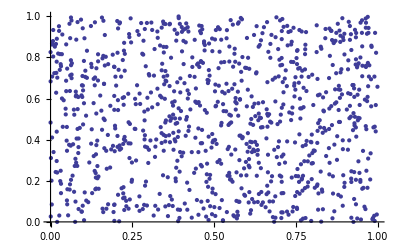

```mathematica
ListPlot[RandomTablePairs[RandomTable[1000],2]]
```

```mathematica
ExpTable[A_,λ_]:= Table[-1/λ * Log[A[[i]]],{i,1,Length[A]}]
```

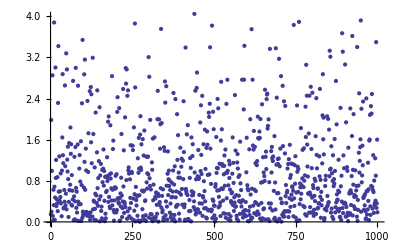

```mathematica
ListPlot[Ex[RandomTable[1000],1]]
```

```mathematica
DistribiutionFunc[x_]:=If[x<.1,-1,If[x<.6,0,If[x≤.9,1]]]
```

```mathematica
DiscreteDistribution[A_]:=Table[DistribiutionFunc[A[[i]]],{i,1,Length[A]}]
```

```mathematica
ListPlot[DiscreteDistribution[RandomTable[1000]]]
```

-Graphics-

```mathematica
Ra
```

```mathematica
DiscreteDistribution[A_]:=Table[DistribiutionFunc[A[[i]]],{i,1,Length[A]}]
```

```mathematica
ListPlot[DiscreteDistribution[RandomTable[1000]]]
```

-Graphics-

```mathematica
DistribiutionFunc[x_]:=If[x<.1,-1,If[x<.6,0,If[x≤.9,1]]]
```

```mathematica
ListPlot[DiscreteDistribution[RandomTable[1000]]]
```

-Graphics-

```mathematica
RandomTable[10]
```

RandomTable[10]

```mathematica
RandomTable[n_] := Table[Random[],{i,1,n}]
```

```mathematica
RandomTable[10]
```

{0.505902,0.0371564,0.912211,0.209868,0.0752116,0.080148,0.93082,0.403522,0.14773,0.324476}

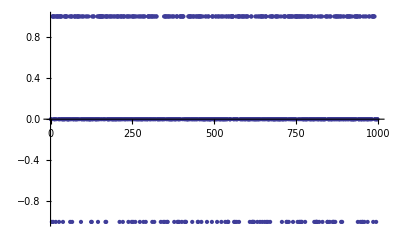

```mathematica
ListPlot[DiscreteDistribution[RandomTable[1000]]]
```